### Imports

```mathematica
(* kill everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\Tal Miller\\Dropbox\\UNI\\Courses Graduate\\QFT\\Papers and Reviews\\Supersymmetric index and Localization\\Thesis\\Notebooks\\Star_shaped_quivers"];
```

```mathematica
<<"CharactersFunctions.m"
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\11.0\\AddOns\\Applications\\LieART\\LieART.m"]
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
maxVarNum=6;
a=Table[Subscript["a",i],{i,maxVarNum}];
b=Table[Subscript["b",i],{i,maxVarNum}];
$Assumptions={r>0,r<1};
```

### SU(3) chars

#### Rep {1,0} (fundamental)

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-a_1 r) (1-r/(a_1 a_2)) (1-a_2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is zero.

Residue for pole 2/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

calculation time = 0.046875 seconds = 0.0000130208 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1

Numeric divergence degree is 0.

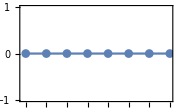

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,0} + Rep {1,0}

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-a_1 r)^2 (1-r/(a_1 a_2))^2 (1-a_2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is zero.

Residue for pole 2/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

calculation time = 0.09375 seconds = 0.0000260417 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is 0.

-Graphics-

#### Rep {1,0} + Rep {0,1}

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
algebraClass=A;
repDynkinLabels={0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[3]

a_1 a_2+1/a_1+1/a_2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r/a_1) (1-a_1 r) (1-r/a_2) (1-r/(a_1 a_2)) (1-a_2 r) (1-a_1 a_2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 1

Calculating residue for pole 2/3 in level 1

Calculating residue for pole 3/3 in level 1

Residue for pole 1/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 2/3 in level 1 is zero.

Residue for pole 3/3 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

calculation time = 0.171875 seconds = 0.0000477431 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

Numeric divergence degree is -0.998006

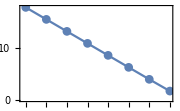

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0}

```mathematica
algebraClass=A;
repDynkinLabels={2,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1^2+a_2 a_1+a_2^2+1/a_2+1/a_1+1/(a_2^2 a_1^2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r/a_1) (1-a_1^2 r) (1-r/(a_1^2 a_2^2)) (1-r/a_2) (1-a_1 a_2 r) (1-a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 1

Calculating residue for pole 2/4 in level 1

Calculating residue for pole 3/4 in level 1

Calculating residue for pole 4/4 in level 1

Residue for pole 1/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 2/4 in level 1 is zero.

Residue for pole 3/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 4/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

calculation time = 0.40625 seconds = 0.000112847 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^3)

Numeric divergence degree is -0.996046

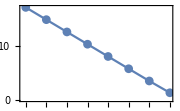

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0} + Rep {2,0}

```mathematica
algebraClass=A;
repDynkinLabels={2,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1^2+a_2 a_1+a_2^2+1/a_2+1/a_1+1/(a_2^2 a_1^2)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r/a_1)^2 (1-a_1^2 r)^2 (1-r/(a_1^2 a_2^2))^2 (1-r/a_2)^2 (1-a_1 a_2 r)^2 (1-a_2^2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 1

Calculating residue for pole 2/4 in level 1

Calculating residue for pole 3/4 in level 1

Calculating residue for pole 4/4 in level 1

Residue for pole 1/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 2/4 in level 1 is zero.

Residue for pole 3/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 4/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

calculation time = 0.5 seconds = 0.000138889 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/((r^3-1)^4)

Numeric divergence degree is -3.98418

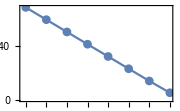

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0} + Rep {0,2}

```mathematica
algebraClass=A;
repDynkinLabels={2,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1^2+a_2 a_1+a_2^2+1/a_2+1/a_1+1/(a_2^2 a_1^2)

```mathematica
algebraClass=A;
repDynkinLabels={0,2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[6]

a_1^2 a_2^2+a_2+a_1+1/a_1^2+1/(a_1 a_2)+1/a_2^2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r/a_1^2) (1-r/a_1) (1-a_1 r) (1-a_1^2 r) (1-r/a_2^2) (1-r/(a_1^2 a_2^2)) (1-r/a_2) (1-r/(a_1 a_2)) (1-a_2 r) (1-a_1 a_2 r) (1-a_2^2 r) (1-a_1^2 a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 1

Calculating residue for pole 2/7 in level 1

Calculating residue for pole 3/7 in level 1

Calculating residue for pole 4/7 in level 1

Calculating residue for pole 5/7 in level 1

Calculating residue for pole 6/7 in level 1

Calculating residue for pole 7/7 in level 1

Residue for pole 1/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 2/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 3/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 2

Calculating residue for pole 2/2 in level 2

Residue for pole 4/7 in level 1 is zero.

Residue for pole 5/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 6/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 7/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

calculation time = 1.89063 seconds = 0.000525174 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/((r-1)^4 (r+1)^2 (r^2+1) (r^2+r+1)^2)

Numeric divergence degree is -3.98422

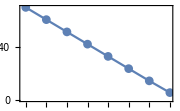

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,1} (adjoint)

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r)^2 (1-r/(a_1 a_2^2)) (1-r/(a_1^2 a_2)) (1-(a_1 r)/a_2) (1-(a_2 r)/a_1) (1-a_1^2 a_2 r) (1-a_1 a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is zero.

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 3/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.796875 seconds = 0.000221354 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(r^5-r^3-r^2+1)

Numeric divergence degree is -1.99405

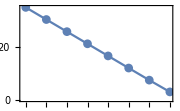

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,1} + Rep {1,1}

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r)^4 (1-r/(a_1 a_2^2))^2 (1-r/(a_1^2 a_2))^2 (1-(a_1 r)/a_2)^2 (1-(a_2 r)/a_1)^2 (1-a_1^2 a_2 r)^2 (1-a_1 a_2^2 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Calculating residue for pole 2/5 in level 1

Calculating residue for pole 3/5 in level 1

Calculating residue for pole 4/5 in level 1

Calculating residue for pole 5/5 in level 1

Residue for pole 1/5 in level 1 is zero.

Residue for pole 2/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 2

Calculating residue for pole 2/9 in level 2

Calculating residue for pole 3/9 in level 2

Calculating residue for pole 4/9 in level 2

Calculating residue for pole 5/9 in level 2

Calculating residue for pole 6/9 in level 2

Calculating residue for pole 7/9 in level 2

Calculating residue for pole 8/9 in level 2

Calculating residue for pole 9/9 in level 2

Residue for pole 3/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 4/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 5/5 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 2.42188 seconds = 0.000672743 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

(r^4-r^2+1)/((r-1)^8 (r+1)^4 (r^2+r+1)^4)

Numeric divergence degree is -7.9828

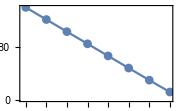

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,1} + Rep {1,0}

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char1+char2,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r)^2 (1-a_1 r) (1-r/(a_1 a_2^2)) (1-r/(a_1^2 a_2)) (1-r/(a_1 a_2)) (1-(a_1 r)/a_2) (1-a_2 r) (1-(a_2 r)/a_1) (1-a_1^2 a_2 r) (1-a_1 a_2^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 1

Calculating residue for pole 2/6 in level 1

Calculating residue for pole 3/6 in level 1

Calculating residue for pole 4/6 in level 1

Calculating residue for pole 5/6 in level 1

Calculating residue for pole 6/6 in level 1

Residue for pole 1/6 in level 1 is zero.

Residue for pole 2/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 3/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 4/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 5/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 6/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 2.625 seconds = 0.000729167 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-((r^2+2) (r^2+r+1))/(3 (r+1)^2 ((r-1) r+1) (r^3-1)^3)

Numeric divergence degree is -2.98697

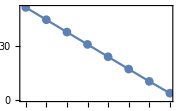

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {3,0}

```mathematica
algebraClass=A;
repDynkinLabels={3,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

10

a_1^3+a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2^3+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+1/(a_2^3 a_1^3)+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r) (1-a_1^3 r) (1-r/(a_1^3 a_2^3)) (1-r/(a_1 a_2^2)) (1-r/(a_1^2 a_2)) (1-(a_1 r)/a_2) (1-(a_2 r)/a_1) (1-a_1^2 a_2 r) (1-a_1 a_2^2 r) (1-a_2^3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 1

Calculating residue for pole 2/8 in level 1

Calculating residue for pole 3/8 in level 1

Calculating residue for pole 4/8 in level 1

Calculating residue for pole 5/8 in level 1

Calculating residue for pole 6/8 in level 1

Calculating residue for pole 7/8 in level 1

Calculating residue for pole 8/8 in level 1

Residue for pole 1/8 in level 1 is zero.

Residue for pole 2/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 3/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 4/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 5/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 2

Calculating residue for pole 2/9 in level 2

Calculating residue for pole 3/9 in level 2

Calculating residue for pole 4/9 in level 2

Calculating residue for pole 5/9 in level 2

Calculating residue for pole 6/9 in level 2

Calculating residue for pole 7/9 in level 2

Calculating residue for pole 8/9 in level 2

Calculating residue for pole 9/9 in level 2

Residue for pole 6/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 7/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 8/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 4.1875 seconds = 0.00116319 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

$Aborted

Numeric divergence degree is -1.98448

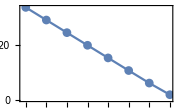

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,1}

```mathematica
algebraClass=A;
repDynkinLabels={2,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

15

a_2 a_1^3+a_2^2 a_1^2+a_1^2/a_2+a_2^3 a_1+2 a_1+2 a_2+1/a_2^2+a_2^2/a_1+2/(a_2 a_1)+1/(a_2^3 a_1^2)+1/a_1^2+1/(a_2^2 a_1^3)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 (1-r/a_1^2) (1-a_1 r)^2 (1-r/(a_1^2 a_2^3)) (1-r/a_2^2) (1-r/(a_1^3 a_2^2)) (1-r/(a_1 a_2))^2 (1-(a_1^2 r)/a_2) (1-a_2 r)^2 (1-a_1^3 a_2 r) (1-(a_2^2 r)/a_1) (1-a_1^2 a_2^2 r) (1-a_1 a_2^3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

```mathematica
calcNumericDivergence[hilbertComponents]
```

```mathematica
(* prohibitive calculation *)
```

### SU(3) + U(1) chars

#### SU(3) rep {1,0} + rep {1,0} with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char1+1/t char2,rankTot]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 t (1-(a_1 r)/t) (1-a_1 r t) (1-r/(a_1 a_2 t)) (1-(r t)/(a_1 a_2)) (1-(a_2 r)/t) (1-a_2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 1

Calculating residue for pole 2/4 in level 1

Calculating residue for pole 3/4 in level 1

Calculating residue for pole 4/4 in level 1

Residue for pole 1/4 in level 1 is zero.

Residue for pole 2/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 3/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

calculation time = 0.421875 seconds = 0.000117188 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is 0.

-Graphics-

#### SU(3) rep {1,0} + rep {0,1} with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
algebraClass=A;
repDynkinLabels={0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[3]

a_1 a_2+1/a_1+1/a_2

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char1+1/t char2,rankTot]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 t (1-r/(a_1 t)) (1-a_1 r t) (1-r/(a_2 t)) (1-(r t)/(a_1 a_2)) (1-a_2 r t) (1-(a_1 a_2 r)/t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 1

Calculating residue for pole 2/4 in level 1

Calculating residue for pole 3/4 in level 1

Calculating residue for pole 4/4 in level 1

Residue for pole 1/4 in level 1 is zero.

Residue for pole 2/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 4/4 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 0.40625 seconds = 0.000112847 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^2)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -0.998006

-Graphics-

#### SU(3) rep {2,0} + rep {0,2} with opposite U(1) charges (Long Haar)

```mathematica
algebraClass=A;
repDynkinLabels={2,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

6

a_1^2+a_2 a_1+a_2^2+1/a_2+1/a_1+1/(a_2^2 a_1^2)

```mathematica
algebraClass=A;
repDynkinLabels={0,2};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char2= dynkinToChar[a,repDynkinLabels,algebraClass]
```

OverBar[6]

a_1^2 a_2^2+a_2+a_1+1/a_1^2+1/(a_1 a_2)+1/a_2^2

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Long"] *charToHilbertIntegrand[cartanVars,r, t char1+1/t char2,rankTot]
```

((1-1/(a_1 a_2^2)) (1-1/(a_1^2 a_2)) (1-a_1/a_2) (1-a_2/a_1) (1-a_1^2 a_2) (1-a_1 a_2^2))/(6 a_1 a_2 t (1-r/(a_1^2 t)) (1-(r t)/a_1) (1-(a_1 r)/t) (1-a_1^2 r t) (1-r/(a_2^2 t)) (1-(r t)/(a_1^2 a_2^2)) (1-(r t)/a_2) (1-r/(a_1 a_2 t)) (1-(a_2 r)/t) (1-a_1 a_2 r t) (1-a_2^2 r t) (1-(a_1^2 a_2^2 r)/t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
hilbertComponents={hilbertComponents};
```

Level = 1

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 1

Calculating residue for pole 2/7 in level 1

Calculating residue for pole 3/7 in level 1

Calculating residue for pole 4/7 in level 1

Calculating residue for pole 5/7 in level 1

Calculating residue for pole 6/7 in level 1

Calculating residue for pole 7/7 in level 1

Residue for pole 1/7 in level 1 is zero.

Residue for pole 2/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 12

Calculating residue for pole 1/12 in level 2

Calculating residue for pole 2/12 in level 2

Calculating residue for pole 3/12 in level 2

Calculating residue for pole 4/12 in level 2

Calculating residue for pole 5/12 in level 2

Calculating residue for pole 6/12 in level 2

Calculating residue for pole 7/12 in level 2

Calculating residue for pole 8/12 in level 2

Calculating residue for pole 9/12 in level 2

Calculating residue for pole 10/12 in level 2

Calculating residue for pole 11/12 in level 2

Calculating residue for pole 12/12 in level 2

Residue for pole 1/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 6/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 7/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 8/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 9/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 10/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 11/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 12/12 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Accumulated sick branches {10,11}/12 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Forming a new list of healty branches in level 2

Residue for pole 3/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 15

Calculating residue for pole 1/15 in level 3

Calculating residue for pole 2/15 in level 3

Calculating residue for pole 3/15 in level 3

Calculating residue for pole 4/15 in level 3

Calculating residue for pole 5/15 in level 3

Calculating residue for pole 6/15 in level 3

Calculating residue for pole 7/15 in level 3

Calculating residue for pole 8/15 in level 3

Calculating residue for pole 9/15 in level 3

Calculating residue for pole 10/15 in level 3

Calculating residue for pole 11/15 in level 3

Calculating residue for pole 12/15 in level 3

Calculating residue for pole 13/15 in level 3

Calculating residue for pole 14/15 in level 3

Calculating residue for pole 15/15 in level 3

Residue for pole 4/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 12

Calculating residue for pole 1/12 in level 3

Calculating residue for pole 2/12 in level 3

Calculating residue for pole 3/12 in level 3

Calculating residue for pole 4/12 in level 3

Calculating residue for pole 5/12 in level 3

Calculating residue for pole 6/12 in level 3

Calculating residue for pole 7/12 in level 3

Calculating residue for pole 8/12 in level 3

Calculating residue for pole 9/12 in level 3

Calculating residue for pole 10/12 in level 3

Calculating residue for pole 11/12 in level 3

Calculating residue for pole 12/12 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 5/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 2

Calculating residue for pole 2/7 in level 2

Calculating residue for pole 3/7 in level 2

Calculating residue for pole 4/7 in level 2

Calculating residue for pole 5/7 in level 2

Calculating residue for pole 6/7 in level 2

Calculating residue for pole 7/7 in level 2

Residue for pole 1/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 3/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 4/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 5/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 6/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 7/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 6/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 7/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 8.8125 seconds = 0.00244792 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

-1/((r^2-1)^3 (r^6+2 r^4+2 r^2+1))

Numeric divergence degree is -2.98249

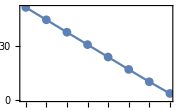

```mathematica
calcNumericDivergence[hilbertComponents]
```

```mathematica
(* The Short Haar version Branches method failed, and Simplify method is prohobitive *)
```

#### SU(3) rep {1,1} + singlet with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 t (1-r/t) (1-r t)^2 (1-(r t)/(a_1 a_2^2)) (1-(r t)/(a_1^2 a_2)) (1-(a_1 r t)/a_2) (1-(a_2 r t)/a_1) (1-a_1^2 a_2 r t) (1-a_1 a_2^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.8125 seconds = 0.000225694 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(r^10-r^6-r^4+1)

```mathematica
calcNumericDivergence[hilbertComponents]
```

Numeric divergence degree is -1.98448

-Graphics-

#### SU(3) rep {1,1} + rep {1,0} with opposite U(1) charges

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
repDynkinLabels={1,0};
dynkinToIrrep[repDynkinLabels,algebraClass]
char1= dynkinToChar[a,repDynkinLabels,algebraClass]
```

3

a_1+a_2+1/(a_2 a_1)

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char1+1/t char2,rankTot]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 t (1-r/(a_1^2 t)) (1-(a_1 r)/t) (1-a_1 r t) (1-r/(a_2^2 t)) (1-r/(a_1 a_2 t)) (1-(r t)/(a_1 a_2)) (1-(a_2 r)/t) (1-a_2 r t) (1-(a_1^2 a_2^2 r)/t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 1

Calculating residue for pole 2/7 in level 1

Calculating residue for pole 3/7 in level 1

Calculating residue for pole 4/7 in level 1

Calculating residue for pole 5/7 in level 1

Calculating residue for pole 6/7 in level 1

Calculating residue for pole 7/7 in level 1

Residue for pole 1/7 in level 1 is zero.

Residue for pole 2/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 1/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 4/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 5/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 6/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Accumulated sick branches {4,5,6}/6 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Forming a new list of healty branches in level 2

Residue for pole 3/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 4/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 3

Calculating residue for pole 2/11 in level 3

Calculating residue for pole 3/11 in level 3

Calculating residue for pole 4/11 in level 3

Calculating residue for pole 5/11 in level 3

Calculating residue for pole 6/11 in level 3

Calculating residue for pole 7/11 in level 3

Calculating residue for pole 8/11 in level 3

Calculating residue for pole 9/11 in level 3

Calculating residue for pole 10/11 in level 3

Calculating residue for pole 11/11 in level 3

Residue for pole 5/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 6/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 7/7 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

calculation time = 5.46875 seconds = 0.0015191 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/(1-r^12)

```mathematica
hilbertComponents
```

Numeric divergence degree is -0.979889

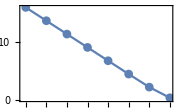

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### SU(3) rep {1,1} + rep {1,1} with opposite U(1) charges (Long Haar)

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Long"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

((1-1/(a_1 a_2^2)) (1-1/(a_1^2 a_2)) (1-a_1/a_2) (1-a_2/a_1) (1-a_1^2 a_2) (1-a_1 a_2^2))/(6 a_1 a_2 t (1-r/t)^2 (1-r t)^2 (1-r/(a_1 a_2^2 t)) (1-(r t)/(a_1 a_2^2)) (1-r/(a_1^2 a_2 t)) (1-(r t)/(a_1^2 a_2)) (1-(a_1 r)/(a_2 t)) (1-(a_1 r t)/a_2) (1-(a_2 r)/(a_1 t)) (1-(a_2 r t)/a_1) (1-(a_1^2 a_2 r)/t) (1-a_1^2 a_2 r t) (1-(a_1 a_2^2 r)/t) (1-a_1 a_2^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 1

Calculating residue for pole 2/8 in level 1

Calculating residue for pole 3/8 in level 1

Calculating residue for pole 4/8 in level 1

Calculating residue for pole 5/8 in level 1

Calculating residue for pole 6/8 in level 1

Calculating residue for pole 7/8 in level 1

Calculating residue for pole 8/8 in level 1

Residue for pole 1/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 2/8 in level 1 is zero.

Residue for pole 3/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 1/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 2/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 3/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 4/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 5/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Residue for pole 6/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Residue for pole 7/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 8/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 14

Calculating residue for pole 1/14 in level 2

Calculating residue for pole 2/14 in level 2

Calculating residue for pole 3/14 in level 2

Calculating residue for pole 4/14 in level 2

Calculating residue for pole 5/14 in level 2

Calculating residue for pole 6/14 in level 2

Calculating residue for pole 7/14 in level 2

Calculating residue for pole 8/14 in level 2

Calculating residue for pole 9/14 in level 2

Calculating residue for pole 10/14 in level 2

Calculating residue for pole 11/14 in level 2

Calculating residue for pole 12/14 in level 2

Calculating residue for pole 13/14 in level 2

Calculating residue for pole 14/14 in level 2

Residue for pole 1/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 6/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 7/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 21

Calculating residue for pole 1/21 in level 3

Calculating residue for pole 2/21 in level 3

Calculating residue for pole 3/21 in level 3

Calculating residue for pole 4/21 in level 3

Calculating residue for pole 5/21 in level 3

Calculating residue for pole 6/21 in level 3

Calculating residue for pole 7/21 in level 3

Calculating residue for pole 8/21 in level 3

Calculating residue for pole 9/21 in level 3

Calculating residue for pole 10/21 in level 3

Calculating residue for pole 11/21 in level 3

Calculating residue for pole 12/21 in level 3

Calculating residue for pole 13/21 in level 3

Calculating residue for pole 14/21 in level 3

Calculating residue for pole 15/21 in level 3

Calculating residue for pole 16/21 in level 3

Calculating residue for pole 17/21 in level 3

Calculating residue for pole 18/21 in level 3

Calculating residue for pole 19/21 in level 3

Calculating residue for pole 20/21 in level 3

Calculating residue for pole 21/21 in level 3

Residue for pole 8/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 9/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 10/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 11/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 12/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 13/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 14/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Accumulated sick branches {9,10}/14 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Forming a new list of healty branches in level 2

Residue for pole 5/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 21

Calculating residue for pole 1/21 in level 3

Calculating residue for pole 2/21 in level 3

Calculating residue for pole 3/21 in level 3

Calculating residue for pole 4/21 in level 3

Calculating residue for pole 5/21 in level 3

Calculating residue for pole 6/21 in level 3

Calculating residue for pole 7/21 in level 3

Calculating residue for pole 8/21 in level 3

Calculating residue for pole 9/21 in level 3

Calculating residue for pole 10/21 in level 3

Calculating residue for pole 11/21 in level 3

Calculating residue for pole 12/21 in level 3

Calculating residue for pole 13/21 in level 3

Calculating residue for pole 14/21 in level 3

Calculating residue for pole 15/21 in level 3

Calculating residue for pole 16/21 in level 3

Calculating residue for pole 17/21 in level 3

Calculating residue for pole 18/21 in level 3

Calculating residue for pole 19/21 in level 3

Calculating residue for pole 20/21 in level 3

Calculating residue for pole 21/21 in level 3

Residue for pole 6/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 1/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 6/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 7/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 8/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 7/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 8/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

calculation time = 19.4219 seconds = 0.00539497 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

$Aborted

```mathematica
hilbertComponents
```

Numeric divergence degree is -6.98036

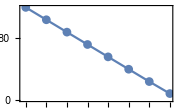

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### SU(3) rep {1,1} + rep {1,1} with opposite U(1) charges (Short Haar)

```mathematica
algebraClass=A;
repDynkinLabels={1,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

a_2 a_1^2+a_2^2 a_1+a_1/a_2+a_2/a_1+1/(a_2^2 a_1)+1/(a_2 a_1^2)+2

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

((1-a_1/a_2) (1-a_1^2 a_2) (1-a_1 a_2^2))/(a_1 a_2 t (1-r/t)^2 (1-r t)^2 (1-r/(a_1 a_2^2 t)) (1-(r t)/(a_1 a_2^2)) (1-r/(a_1^2 a_2 t)) (1-(r t)/(a_1^2 a_2)) (1-(a_1 r)/(a_2 t)) (1-(a_1 r t)/a_2) (1-(a_2 r)/(a_1 t)) (1-(a_2 r t)/a_1) (1-(a_1^2 a_2 r)/t) (1-a_1^2 a_2 r t) (1-(a_1 a_2^2 r)/t) (1-a_1 a_2^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 1

Calculating residue for pole 2/8 in level 1

Calculating residue for pole 3/8 in level 1

Calculating residue for pole 4/8 in level 1

Calculating residue for pole 5/8 in level 1

Calculating residue for pole 6/8 in level 1

Calculating residue for pole 7/8 in level 1

Calculating residue for pole 8/8 in level 1

Residue for pole 1/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 2

Calculating residue for pole 2/4 in level 2

Calculating residue for pole 3/4 in level 2

Calculating residue for pole 4/4 in level 2

Residue for pole 1/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 3/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 4/4 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 2/8 in level 1 is zero.

Residue for pole 3/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 1/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 2/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 3/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 4/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Residue for pole 5/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Residue for pole 6/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 7/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 8/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 4/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 14

Calculating residue for pole 1/14 in level 2

Calculating residue for pole 2/14 in level 2

Calculating residue for pole 3/14 in level 2

Calculating residue for pole 4/14 in level 2

Calculating residue for pole 5/14 in level 2

Calculating residue for pole 6/14 in level 2

Calculating residue for pole 7/14 in level 2

Calculating residue for pole 8/14 in level 2

Calculating residue for pole 9/14 in level 2

Calculating residue for pole 10/14 in level 2

Calculating residue for pole 11/14 in level 2

Calculating residue for pole 12/14 in level 2

Calculating residue for pole 13/14 in level 2

Calculating residue for pole 14/14 in level 2

Residue for pole 1/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 6/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 7/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 21

Calculating residue for pole 1/21 in level 3

Calculating residue for pole 2/21 in level 3

Calculating residue for pole 3/21 in level 3

Calculating residue for pole 4/21 in level 3

Calculating residue for pole 5/21 in level 3

Calculating residue for pole 6/21 in level 3

Calculating residue for pole 7/21 in level 3

Calculating residue for pole 8/21 in level 3

Calculating residue for pole 9/21 in level 3

Calculating residue for pole 10/21 in level 3

Calculating residue for pole 11/21 in level 3

Calculating residue for pole 12/21 in level 3

Calculating residue for pole 13/21 in level 3

Calculating residue for pole 14/21 in level 3

Calculating residue for pole 15/21 in level 3

Calculating residue for pole 16/21 in level 3

Calculating residue for pole 17/21 in level 3

Calculating residue for pole 18/21 in level 3

Calculating residue for pole 19/21 in level 3

Calculating residue for pole 20/21 in level 3

Calculating residue for pole 21/21 in level 3

Residue for pole 8/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 9/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 10/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Residue calculation failed.

Failed residue exists in level 3, return "failed" flag

Residue for pole 11/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 12/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Residue for pole 13/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 14/14 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Accumulated sick branches {9,10}/14 in level2

Summing and simplifying the sick branches.

Resending to level3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Forming a new list of healty branches in level 2

Residue for pole 5/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 21

Calculating residue for pole 1/21 in level 3

Calculating residue for pole 2/21 in level 3

Calculating residue for pole 3/21 in level 3

Calculating residue for pole 4/21 in level 3

Calculating residue for pole 5/21 in level 3

Calculating residue for pole 6/21 in level 3

Calculating residue for pole 7/21 in level 3

Calculating residue for pole 8/21 in level 3

Calculating residue for pole 9/21 in level 3

Calculating residue for pole 10/21 in level 3

Calculating residue for pole 11/21 in level 3

Calculating residue for pole 12/21 in level 3

Calculating residue for pole 13/21 in level 3

Calculating residue for pole 14/21 in level 3

Calculating residue for pole 15/21 in level 3

Calculating residue for pole 16/21 in level 3

Calculating residue for pole 17/21 in level 3

Calculating residue for pole 18/21 in level 3

Calculating residue for pole 19/21 in level 3

Calculating residue for pole 20/21 in level 3

Calculating residue for pole 21/21 in level 3

Residue for pole 6/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 2

Calculating residue for pole 2/8 in level 2

Calculating residue for pole 3/8 in level 2

Calculating residue for pole 4/8 in level 2

Calculating residue for pole 5/8 in level 2

Calculating residue for pole 6/8 in level 2

Calculating residue for pole 7/8 in level 2

Calculating residue for pole 8/8 in level 2

Residue for pole 1/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 4/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 6/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 7/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 8/8 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 7/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 8/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

calculation time = 13.0781 seconds = 0.00363281 hours

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Numeric divergence degree is 0.

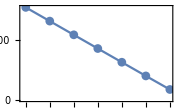

```mathematica
calcNumericDivergence[hilbertComponents]
```

```mathematica
(* the Simplify method is prohibitive *)
```

```mathematica
(* The Short Haar gives 0 and Long Haar gives 7, dont know why *)
```